```mathematica
双直导线在一些方向产生的磁场分布
```

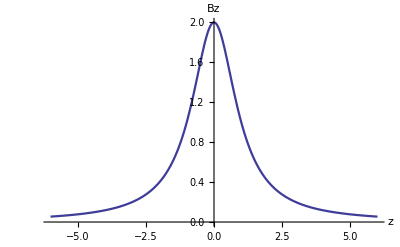

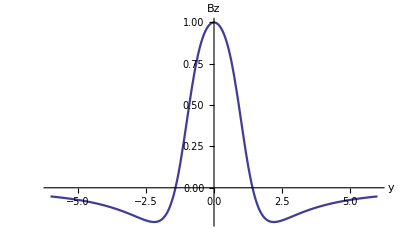

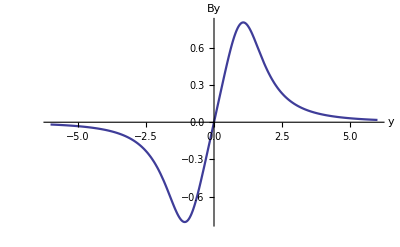

-Graphics3D-

```mathematica
By[y_,z_]:=(1/((d/2-y)^2+z^2)-1/((d/2+y)^2+z^2)) z;
Bz[y_,z_]:=(d/2-y)/((d/2-y)^2+z^2)+(d/2+y)/((d/2+y)^2+z^2);d=2;
Plot[Bz[0,z],{z,-3d,3d},
AxesLabel->{"z","Bz"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[Bz[y,d/2],{y,-3d,3d},
AxesLabel->{"y","Bz"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[By[y,d/2],{y,-3d,3d},
AxesLabel->{"y","By"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot3D[By[y,z],{y,-3d,3d},{z,-3d,3d},
PlotRange->All,PlotPoints->100,Mesh->False,
AxesLabel->{"y","z","By"},
AxesStyle->Thickness[0.003]]
Clear[d,Bz,By]
```